```mathematica
Quit
```

## Numerical Triangle

### Solution’s upload

```mathematica
(*Kottler*)
EqmAdim=-x^3+x^5 Λb+x^4 f'[x]-12 x λb f'[x]^2-24 λb f[x]^2 (2 f'[x]+x (-2 f''[x]+x Derivative[3][f][x]))+f[x] (48 x λb f'[x]^2+12 λb f'[x] (4-4 x^2 f''[x]+x^3 Derivative[3][f][x])+x (x^2-48 λb f''[x]+12 x^2 λb f''[x]^2+24 x λb Derivative[3][f][x]))/.λb->0;
fNum=NDSolve[{EqmAdim==0,f[1]==0}/.Λb->1.5*10^(-32),f,{x,1,50}];
fUNum[u_]:=(f[1/u]/. fNum[[1]]);(*Cambio de x->1/u*)
```

```mathematica
(*Einstein Cubic Gravity*)
solY0=Import["Data/sol_y0.txt","Table"]//Flatten;
solY1=Import["Data/sol_y1.txt","Table"]//Flatten;
solT=Import["Data/sol_t.txt","Table"]//Flatten;
ECGSol=Interpolation[Transpose[{solT,solY0}]]; (*La hago una función Continua*)
fUECG[u_]:=ECGSol[1/u](*Cambio de x->1/u*)
```

InterpolatingFunction::dmval: Input value {0.100202} lies outside the range of data in the interpolating function. Extrapolation will be used.

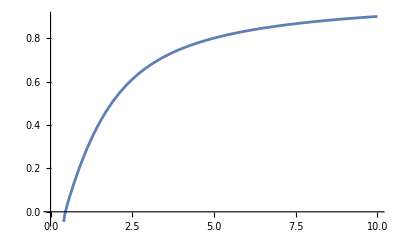

```mathematica
Plot[ECGSol[x],{x,0.1,10},AxesOrigin->{0,0}]
```

### Creación de Triángulos

```mathematica
Θ=0.35; (*Angle Shift*)
b=15; (*Parámetro de Impacto*)
ϵ=1/b; (*El inverso del parámetro de Impacto*)
δ=1.22  ;(*Desplazamiento angular para los lados adyacentes*)
ϕmin=Θ (*π/2-δ*) (*ángulo inicial para lado izquierdo*)
ϕmax=π-ϕmin(*ángulo inicial para lado derecho*)
b1= 1.5  b ;ϵ1= 1/b1;(*parámetro de impacto de los lados adyacentes*)
```

0.35

2.79159

```mathematica
(*Kottler Triangle*)
u0=FindRoot[ϵ^2-fUNum[u]*u^2==0,{u,ϵ}][[1,2]] (*Conditioin u'[π/2]==0*)
```

0.0690966

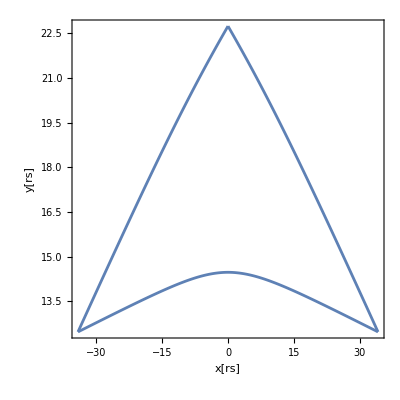

```mathematica
(*Main Geodesic (Triangle Base)*)
(*Initial condition value must be set on hand*)
C1PhiMinKot=NDSolve[{(u'[ϕ])^2-ϵ^2+fUNum[u[ϕ]]*u[ϕ]^2==0,u[π/2]==0.06909655},u,{ϕ,π/2,Θ},Method->{"EquationSimplification"->"Residual"}];
C1PhiMaxKot = NDSolve[{(u'[ϕ])^2-ϵ^2+fUNum[u[ϕ]]*u[ϕ]^2==0,u[π/2]==0.06909655},u,{ϕ,π/2,π-Θ},Method->{"EquationSimplification"->"Residual"}];
(*Lados Adyacentes de triángulos*)
C2Kot=NDSolve[{(u'[ϕ])^2==ϵ1^2-fUNum[u[ϕ]]*u[ϕ]^2,u[ϕmin]==(u[ϕ]/.C1PhiMinKot/.ϕ->ϕmin)[[1]]},u,{ϕ,ϕmin,π/2},Method->{"EquationSimplification"->"Residual"}];
C3Kot = NDSolve[{(u'[ϕ])^2==ϵ1^2-fUNum[u[ϕ]]*u[ϕ]^2,u[ϕmax]==(u[ϕ]/.C1PhiMaxKot/.ϕ->ϕmax)[[1]]},u,{ϕ,π/2,ϕmax},Method->{"EquationSimplification"->"Residual"}];
(*Ploting*)
PltC1Kot=Show[ParametricPlot[{1/u[ϕ] Cos[ϕ],1/u[ϕ] Sin[ϕ]}/.C1PhiMaxKot,{ϕ,π/2,π-Θ}],ParametricPlot[{1/u[ϕ] Cos[ϕ],1/u[ϕ] Sin[ϕ]}/.C1PhiMinKot,{ϕ,π/2,Θ}],PlotRange->All,AspectRatio->1,Frame->True,FrameLabel->{"x[rs]","y[rs]"}];
PltC2Kot=ParametricPlot[{1/u[ϕ] Cos[ϕ],1/u[ϕ] Sin[ϕ]}/.C2Kot,{ϕ,ϕmin,π/2}];
PltC3Kot = ParametricPlot[{1/u[ϕ] Cos[ϕ],1/u[ϕ] Sin[ϕ]}/.C3Kot,{ϕ,π/2,ϕmax}];
YLim =(( 1/u[ϕ]Sin[ϕ])*(1.001)/.C2Kot/.ϕ->π/2)[[1]]; YLimInf = (1/u[ϕ]Sin[ϕ]*(0.999)/.C1PhiMinKot/.ϕ->π/2)[[1]];
XLimL = ((1/u[ϕ] Cos[ϕ])*(1.001)/.C3Kot/.ϕ->ϕmax)[[1]]; XLimR=((1/u[ϕ] Cos[ϕ])*(1.001)/.C2Kot/.ϕ->ϕmin)[[1]];
(*Triangle Plot*)
KotTri=Show[PltC1Kot,PltC2Kot, PltC3Kot,AspectRatio->1,(*PlotRange->{{XLimL,XLimR},{Automatic}}{YLimInf,YLim}},*)Frame->True,FrameLabel->{"x[rs]","y[rs]"}]
```

```mathematica
(* Einstein Cubic Gravity, λ=0.05*)
x0=FindRoot[ϵ^2-fUECG[u]*u^2==0,{u,ϵ}][[1,2]]
```

0.297814

```mathematica
(*Triangle Base*)
C1PhiMinECG=NDSolve[{(u'[ϕ])^2-ϵ^2+fUECG[u[ϕ]]*u[ϕ]^2==0,u[π/2]==0.2978138},u,{ϕ,π/2,Θ},Method->{"EquationSimplification"->"Residual"}];
C1PhiMaxECG = NDSolve[{u'[ϕ]^2-ϵ^2+fUECG[u[ϕ]]*u[ϕ]^2==0,u[π/2]==0.2978138},u,{ϕ,π/2,π-Θ},Method->{"EquationSimplification"->"Residual"}];
(*Adjacent Sides*)
C3ECG=NDSolve[{(u'[ϕ])^2==ϵ1^2-fUECG[u[ϕ]]*u[ϕ]^2,u[ϕmax]==((u[ϕ]/.C1PhiMaxECG/.ϕ->ϕmax)[[1]])},u,{ϕ,ϕmax,π/2},Method->{"EquationSimplification"->"Residual"}];
C2ECG=NDSolve[{(u'[ϕ])^2==ϵ1^2-fUECG[u[ϕ]]*u[ϕ]^2,u[ϕmin]==(u[ϕ]/.C1PhiMinECG/.ϕ->ϕmin)[[1]]},u,{ϕ,ϕmin,π/2},Method->{"EquationSimplification"->"Residual"}];
(*Ploting*)
PltC1ECG=Show[ParametricPlot[{1/u[ϕ] Cos[ϕ],1/u[ϕ] Sin[ϕ]}/.C1PhiMinECG,{ϕ,π/2,Θ},PlotStyle->{Black,Dashed}],ParametricPlot[{1/u[ϕ] Cos[ϕ],1/u[ϕ] Sin[ϕ]}/.C1PhiMaxECG,{ϕ,π/2,π-Θ},PlotStyle->{Black,Dashed}],AspectRatio->1,PlotRange->All,Frame->True,FrameLabel->{"x[rs]","y[rs]"}];
PltC3ECG=ParametricPlot[{1/u[ϕ] Cos[ϕ],1/u[ϕ] Sin[ϕ]}/.C3ECG,{ϕ,π/2,ϕmax},AspectRatio->1,PlotStyle->{Black,Dashed}];
PltC2ECG =ParametricPlot[{1/u[ϕ] Cos[ϕ],1/u[ϕ] Sin[ϕ]}/.C2ECG,{ϕ,π/2,ϕmin},AspectRatio->1,PlotStyle->{Black,Dashed}];
xmin=(1/u[ϕ] Cos[ϕ] 1.001/.C3ECG/.ϕ->ϕmax)[[1]]; xmax=(1/u[ϕ] Cos[ϕ] 1.001/.C2ECG/.ϕ->ϕmin)[[1]];
ymin = (1/u[ϕ] Sin[ϕ] 0.999 /.C1PhiMinECG/.ϕ->π/2)[[1]];ymax = (1/u[ϕ] Sin[ϕ] 1.001 /.C2ECG/.ϕ->π/2)[[1]];
ECGTrian=Show[PltC1ECG,PltC3ECG,PltC2ECG,AspectRatio->1(*,PlotRange->{{xmin,xmax},{ymin,ymax}}*)] ;(*Plot Final del Triángulo*)
ECGFunctions = {C1PhiMinECG,C1PhiMaxECG,C3ECG,C2ECG};
```

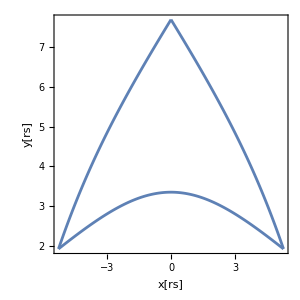
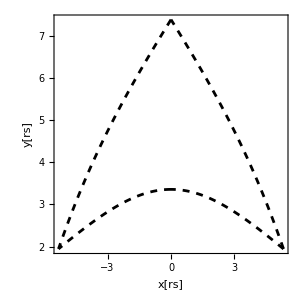
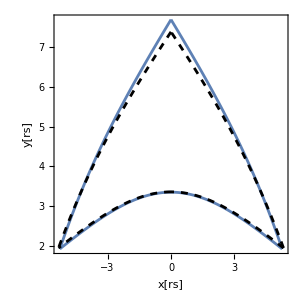
-Graphics-Kottler-Graphics-ECG-Graphics-Both Triangles

```mathematica
Row[{Labeled[Show[KotTri,ImageSize->300],Style["Kottler",16,Bold,Black],Top],Labeled[Show[ECGTrian,ImageSize->300],Style["ECG",16,Bold,Black],Top],Labeled[Show[KotTri,ECGTrian,ImageSize->300],Style["Both Triangles",16,Bold,Black],Top]},Alignment->Center]
```

### Export Data to Python

```mathematica
(*Nos llevamos los triángulos a Python en formato txt*)

(*Angulos*)
AngleC1PhiMin=Subdivide[Θ,π/2,1000]//N;
AngleC1PhiMax=Subdivide[π/2,π-Θ,1000]//N;
AngleC3=Subdivide[π/2,ϕmax,1000]//N;
AngleC2=Subdivide[ϕmin,π/2,1000]//N;
Angles = {AngleC1PhiMin,AngleC1PhiMax,AngleC3,AngleC2};
(*Kottler*)
RKotC1PhiMin=Table[1/u[ϕ]/.C1PhiMinKot/.ϕ->AngleC1PhiMin[[i]],{i,1,Length[AngleC1PhiMin]}]//Flatten;
RKotC1PhiMax=Table[1/u[ϕ]/.C1PhiMaxKot/.ϕ->AngleC1PhiMax[[i]],{i,1,Length[AngleC1PhiMax]}]//Flatten;
RKotC2 = Table[1/u[ϕ]/.C2Kot/.ϕ->AngleC2[[i]],{i,1,Length[AngleC2]}]//Flatten;
RKotC3 = Table[1/u[ϕ]/.C3Kot/.ϕ->AngleC3[[i]],{i,1,Length[AngleC3]}]//Flatten;
(*Exportación a archivos de texto*)
Data={AngleC1PhiMin,AngleC1PhiMax,AngleC3,AngleC2,RKotC1PhiMin,RKotC1PhiMax,RKotC2,RKotC3};
NamesData={"Angle_C1_PhiMin_b4.txt","Angle_C1_PhiMax_b4.txt","Angle_C3_Phi_b4.txt","Angle_C2_Phi_b4.txt","Kottler_R_C1_PhiMin_b4.txt","Kottler_R_C1_PhiMax_b4.txt","Kottler_R_C2_b4.txt","Kottler_R_C3_b4.txt"};
Rute ="Import Rute"; 
Table[Export[Rute<>NamesData[[i]],Data[[i]],"Table"],{i,1,Length[Data]}];
(*Einstein Cubic Gravity*)
ECGData=Table[1/u[ϕ]/.ECGFunctions[[j]]/.ϕ->Angles[[j,i]]//Flatten,{j,1,Length[ECGFunctions]},{i,1,Length[Angles[[j]]]}];
(*ECGData=[C1PhiMinECG (Bottom Right), C1PhiMaxECG (BottomLeft),C3ECG, C2ECG]*)
Table[ ECGData[[i]]=Flatten[ECGData[[i]]],{i,1,4}];
(*Exportación a archivos de texto*)
NamesECG={"ECG_R_C1_PhiMin_b4.txt","ECG_R_C1_PhiMax_b4.txt","ECG_R_C3_b4.txt","ECG_R_C2_b4.txt"};
Rute="Import Rute";
Table[Export[Rute<>NamesECG[[i]],ECGData[[i]],"Table"],{i,1,Length[ECGData]}];
```

```mathematica
Append[NamesData,NamesECG]//Flatten//FortranForm
```

```mathematica
List("Angle_C1_PhiMin_b4.txt","Angle_C1_PhiMax_b4.txt","Angle_C3_Phi_b4.txt","Angle_C2_Phi_b4.txt","Kottler_R_C1_PhiMin_b4.txt","Kottler_R_C1_PhiMax_b4.txt","Kottler_R_C2_b4.txt",
     -  "Kottler_R_C3_b4.txt","ECG_R_C1_PhiMin_b4.txt","ECG_R_C1_PhiMax_b4.txt","ECG_R_C3_b4.txt","ECG_R_C2_b4.txt")
```

### Diferencia Angular

```mathematica
Angle[Sol_,f_,ϕv_]:=180/π (ArcTan[-u[ϕ] Sqrt[f[u[ϕ]]]D[u[ϕ],ϕ]^(-1) ])/.Sol/.ϕ->ϕv
```

```mathematica
(*β1=C3-C1|ϕmax  β2=C1-C2|ϕmin  β3=C2-C3|π/2*)
```

```mathematica
β1Kot = (Angle[C3Kot,fUNum,ϕmax]-Angle[C1PhiMaxKot,fUNum,ϕmax])
β2Kot=(Angle[C1PhiMinKot,fUNum,ϕmin]-Angle[C2Kot,fUNum,ϕmin])
β3Kot = (Angle[C2Kot,fUNum,π/2]-Angle[C3Kot,fUNum,π/2])
βsKot=β1Kot+β2Kot+β3Kot;
β1ECG = (Angle[C3ECG,fUECG,ϕmax]-Angle[C1PhiMaxECG,fUECG,ϕmax])
β2ECG=(Angle[C1PhiMinECG,fUECG,ϕmin]-Angle[C2ECG,fUECG,ϕmin])
β3ECG= (Angle[C2ECG,fUECG,π/2]-Angle[C3ECG,fUECG,π/2])
βsECG=β1ECG+β2ECG+β3ECG;
Abs[βsKot-βsECG]
```

{13.5874}

{13.5874}

{148.339}

{13.8248}

{13.8248}

{147.101}

{0.763443}

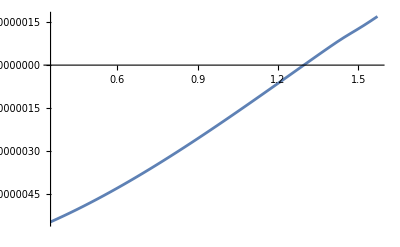

```mathematica
Plot[(u[ϕ]/.C2ECG)-(u[ϕ]/.C2Kot),{ϕ,π/2,ϕmin}]
```

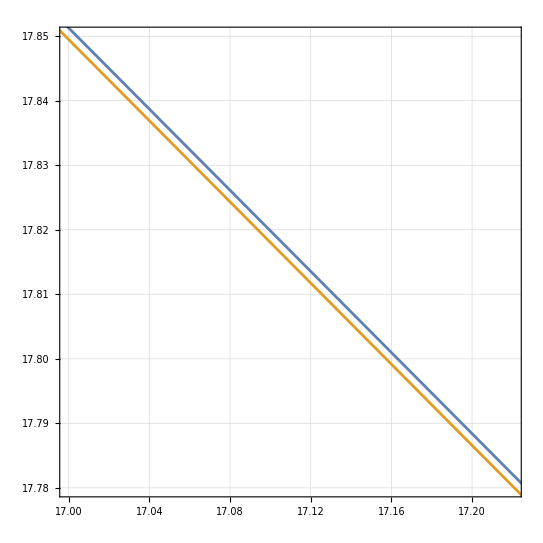

```mathematica
ParametricPlot[{{1/u[ϕ] Cos[ϕ],1/u[ϕ] Sin[ϕ]}/.C2ECG,{1/u[ϕ] Cos[ϕ],1/u[ϕ] Sin[ϕ]}/.C2Kot},{ϕ,π/2,ϕmin},AspectRatio->1,PlotRange->{{17,17.22},{17.78,17.85}},GridLines->Automatic,Frame->True]
```

```mathematica
({Cos[ϕ] 1/u[ϕ],1/u[ϕ] Sin[ϕ]}/.C2Kot/.ϕ->1.3965/2//Flatten)
{Cos[ϕ] 1/u[ϕ],1/u[ϕ] Sin[ϕ]}/.C2Kot/.ϕ->π/2//Flatten
```

{20.0959,16.8665}

{0.,22.7801}

```mathematica
(π/2-ϕmin/2)/2
```

0.697699